#### Problema 4

X_n=Piecewise[{{n (-1+n ω), 0≤ω<1/n}, {0, 1/n≤ω<2}, {1, 2≤ω<n}, {n, ω≥n}}]

Definición la variable aleatoria mediante una función a trozos

Comando: Piecewise

```mathematica
Xn[n_,ω_]:=Piecewise[{{n(n ω-1),0<=ω<1/n},{0,1/n<=ω<2},{1,2≤ω<n},{n,ω≥n}}]
```

```mathematica
Xn[n,ω]
```

Piecewise[{{n (-1+n ω), 0≤ω<1/n}, {0, 1/n≤ω<2}, {1, 2≤ω<n}, {n, ω≥n}, {0, True}}]

Definición de la probabilidad
 P[0,ω]=1-ⅇ^-λω

```mathematica
ProbabilidadOmega[λ_,ω_]:=CDF[ExponentialDistribution[Xn[n,ω]],ω]
```

Construcción del modelo F_n

Comando: TransformedDistribution

```mathematica
TransformedDistribution[Xn[n,Omega],Omega\[Distributed]ExponentialDistribution[λ]]
```

TransformedDistribution[Piecewise[{{n (-1+n Omega), 0≤Omega<1/n}, {0, 1/n≤Omega<2}, {1, 2≤Omega<n}, {n, Omega≥n}, {0, True}}],Omega\[Distributed]ExponentialDistribution[λ]]

No simplifica bien

Definición de  F_n directamente

Comando: Probability

```mathematica
Fn[x_,n_,λ_]:=Probability[Xn[n,Omega]≤x,Omega\[Distributed]ExponentialDistribution[λ],Assumptions-> n≥3]
```

```mathematica
Fn[x,n,λ]
```

Piecewise[{{1, n-x≤0}, {ⅇ^(-2 λ) (-1+ⅇ^(2 λ)), 0≤x<1}, {ⅇ^(-n λ) (-1+ⅇ^(n λ)), x≥1&&n-x>0}, {ⅇ^(-((n+x) λ)/n^2) (-1+ⅇ^(((n+x) λ)/n^2)), n+x>0&&x<0}, {0, True}}]

Limite de la sucesión de funciones de distribución y convergencia débil

Comando: DiscreteLimit

```mathematica
DiscreteLimit[Fn[x,n,λ],n->∞,Assumptions-> λ>0]
```

Piecewise[{{1, x≥1}, {1-ⅇ^(-2 λ), 0≤x<1}, {0, True}}]

Limite de la sucesión de variables aleatorias  y convergencia en distribución

```mathematica
Xlimit[ω_]:=DiscreteLimit[Xn[n,ω],n->∞]
```

```mathematica
Xlimit[ω]
```

Piecewise[{{1, ω≥2}, {-∞, ω==0}, {0, True}}]

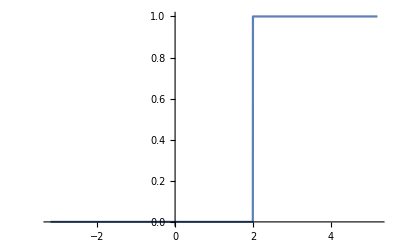

```mathematica
Plot[Xlimit[ω],{ω,-3.2,5.2}]
```

```mathematica
TransformedDistribution[Xlimit[Omega],Omega\[Distributed]ExponentialDistribution[λ]]
```

TransformedDistribution[Piecewise[{{1, x≥2}, {-∞, x==0}, {0, True}}],x\[Distributed]ExponentialDistribution[λ]]

```mathematica
CDF[TransformedDistribution[Piecewise[{{1,x≥2},{-∞,x==0}},0],x\[Distributed]ExponentialDistribution[λ]],x]
```

Piecewise[{{1, x≥1}, {ⅇ^(-2 λ) (-1+ⅇ^(2 λ)), 0≤x<1}, {0, True}}]

```mathematica
Simplify[Piecewise[{{1,x≥1},{ⅇ^(-2 λ) (-1+ⅇ^(2 λ)),0≤x<1}},0]]
```

Piecewise[{{1, x≥1}, {1-ⅇ^(-2 λ), 0≤x<1}, {0, True}}]

Gráficas (no entra en examen)

Gráfica de X_3

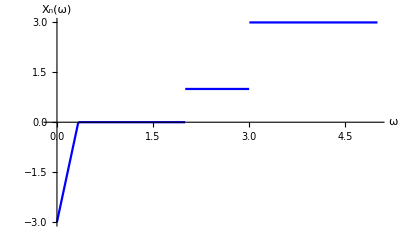

```mathematica
Plot[Xn[3,ω],{ω,0,5},PlotStyle->Blue,PlotRange->{{-0.1,5},All},AxesLabel->{ω,Subscript[X, n][ω]}]
```

Gráfica de X_n arreglada

Dibujar límites de funciones discontinuas con DiscretePlot y PlotMarkers

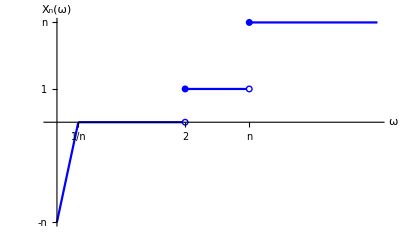

```mathematica
Show[
Plot[Xn[3,x],{x,0,5},PlotStyle->Blue],
DiscretePlot[Limit[Xn[3,t],{t->x},Direction->"FromBelow"],{x,{2,3}},PlotMarkers->"Empty",PlotStyle->Blue,Filling->None],
DiscretePlot[Xn[3,x],{x,{2,3}},PlotMarkers->"Filled",PlotStyle->Blue,Filling->None],
Ticks->{{{1/3,1/n},{2,2},{3,n}},{{-3,-n},{1,1},{3,n}}},
PlotRange->{{-0.1,5},All},AxesLabel->{ω,Subscript[X, n][ω]}]
```

Imagen inversa de X_n

```mathematica
InverseFunction[n(n #-1)&]
```

(n+#1)/n^2&

Dibujar  líneas sobre una gráfica y modificar los ejes

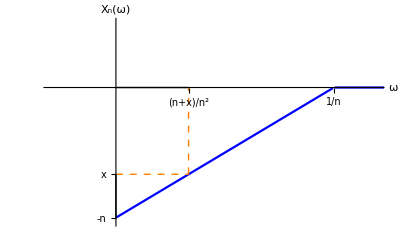

```mathematica
Show[Plot[Xn[3,u],{u,0,4},PlotStyle->Blue],
Graphics[{
Thick,
Line[{{0,-2},{0,-3}}],
Line[{{0,0},{1/9,0}}],
Orange,Thin,Dashed,
Line[{{0,-2},{1/9,-2}}],
Line[{{1/9,-2},{1/9,0}}]
}],
PlotRange->{{-0.1,0.4},{-3.1,1.5}},AxesOrigin->{0,0},Ticks->{{{1/9,(x+n)/n^2},{1/3,1/n}},{{-3,-n},{-2,x}}},AxesLabel->{ω,Subscript[X, n][ω]}]
```

Funciones de distribución

```mathematica
Fn[n_,x_]:=Piecewise[{{1-ⅇ^((-(x+n))/n^2),-n≤x<0},{1-ⅇ^-2,0≤x<1},{1-ⅇ^-n,1≤x<n},{1,x≥n}}]
```

```mathematica
Fn[n_,x_]
```

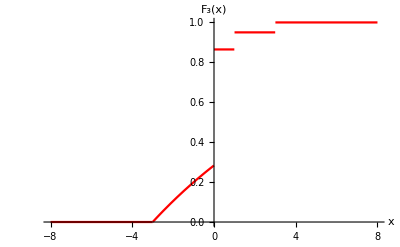

```mathematica
Plot[Fn[3,x],{x,-8,8},PlotStyle->Red,AxesLabel->{x,Subscript[F, 3][x]}]
```

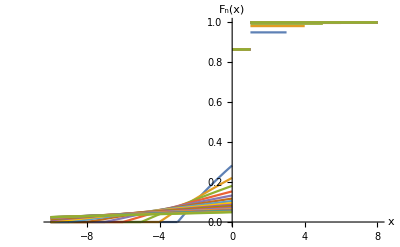

```mathematica
Plot[Evaluate[Table[Fn[n,x],{n,3,20}],{x,-10,8}],
AxesLabel->{x,Subscript[F, n][x]}]
```

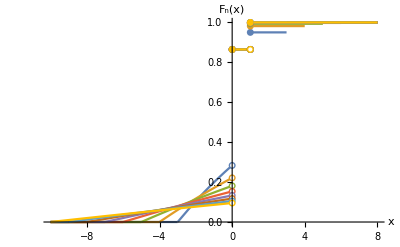

```mathematica
Show[
Plot[Evaluate[Table[Fn[n,x],{n,3,10}]],{x,-10,8}],DiscretePlot[Evaluate[Table[Limit[Fn[n,t],t->0,Direction->"FromBelow"],{n,3,10}]],{x,{0}},PlotMarkers->"Empty",
Filling->None],
DiscretePlot[Evaluate[Table[Limit[Fn[n,t],t->1,Direction->"FromBelow"],{n,3,10}]],{x,{1}},PlotMarkers->"Empty",Filling->None],
DiscretePlot[Evaluate[Table[Fn[n,x],{n,3,10}]],{x,{0,1}},PlotMarkers->"Filled",Filling->None],
AxesLabel->{x,Subscript[F, n][x]}]
```